```mathematica
(* Gaseous phase partition function *)
```

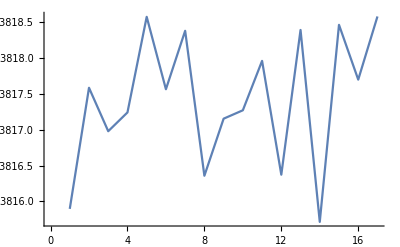

```mathematica
Block[
{MonteCarloSum,n=2*10^4,k=1.38*10^(-23),T,P=9*10^5,q=1.6*10^(-19),m=10^(-26),h=6.63*10^(-34),E0=10^15},
MonteCarloSum[n_,P_,T_,q_,m_,h_,E0_]:=Block[
{r,s,A,sum,sum1},
sum=0;
A={};
r=0;
While[
True,
r=r+1;
s=RandomVariate[BinomialDistribution[n,(n/2-1)/n]];
If[MemberQ[A,s],Continue[],AppendTo[A,s]];
sum1=sum;
sum=sum+Binomial[n,s]*(-1)^s*(k T/108/P(36 HypergeometricPFQ[{1},{1/3,2/3},-(q E0)^3(s+n)^3/1728/(k T)^2/P]+π Sqrt[k T/P](q E0 (s+n)/k/T)^(3/2)(BesselJ[1/3,1/12Sqrt[k T/3/P](q E0(s+n)/k/T)^(3/2)]-BesselJ[-1/3,1/12Sqrt[k T/3/P](q E0(s+n)/k/T)^(3/2)])));
If[Abs[sum1-sum]/Abs[sum1+0.01]<10^(-3),Break[]];
];
Return[sum];
];
ListLinePlot[Table[Log[Abs[MonteCarloSum[n,P,T,q,m,h,E0]]],{T,200,1000,50}]]//Print;
]
```

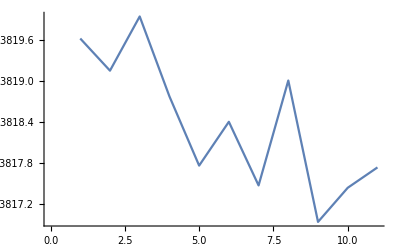

```mathematica
Block[
{MonteCarloSum,n=2*10^4,k=1.38*10^(-23),T=800,P,q=1.6*10^(-19),m=10^(-26),h=6.63*10^(-34),E0=10^15},
MonteCarloSum[n_,P_,T_,q_,m_,h_,E0_]:=Block[
{r,s,A,sum,sum1},
sum=0;
A={};
r=0;
While[
True,
r=r+1;
s=RandomVariate[BinomialDistribution[n,(n/2-1)/n]];
If[MemberQ[A,s],Continue[],AppendTo[A,s]];
sum1=sum;
sum=sum+Binomial[n,s]*(-1)^s*(k T/108/P(36 HypergeometricPFQ[{1},{1/3,2/3},-(q E0)^3(s+n)^3/1728/(k T)^2/P]+π Sqrt[k T/P](q E0 (s+n)/k/T)^(3/2)(BesselJ[1/3,1/12Sqrt[k T/3/P](q E0(s+n)/k/T)^(3/2)]-BesselJ[-1/3,1/12Sqrt[k T/3/P](q E0(s+n)/k/T)^(3/2)])));
If[Abs[sum1-sum]/Abs[sum1+0.01]<10^(-3),Break[]];
];
Return[sum];
];
ListLinePlot[Table[Log[Abs[MonteCarloSum[n,P,T,q,m,h,E0]]],{P,10^5,10^6,0.9*10^5}]]//Print;
]
```

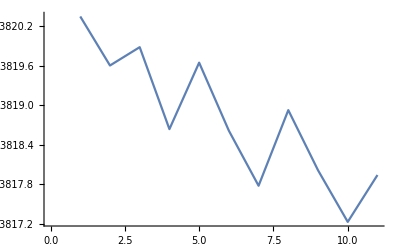

```mathematica
Block[
{MonteCarloSum,n=2*10^4,k=1.38*10^(-23),T=800,P,q=1.6*10^(-19),m=10^(-26),h=6.63*10^(-34),E0=10^15},
MonteCarloSum[n_,P_,T_,q_,m_,h_,E0_]:=Block[
{r,s,A,sum,sum1},
sum=0;
A={};
r=0;
While[
True,
r=r+1;
s=RandomVariate[BinomialDistribution[n,(n/2-1)/n]];
If[MemberQ[A,s],Continue[],AppendTo[A,s]];
sum1=sum;
sum=sum+Binomial[n,s]*(-1)^s*(k T/108/P(36 HypergeometricPFQ[{1},{1/3,2/3},-(q E0)^3(s+n)^3/1728/(k T)^2/P]+π Sqrt[k T/P](q E0 (s+n)/k/T)^(3/2)(BesselJ[1/3,1/12Sqrt[k T/3/P](q E0(s+n)/k/T)^(3/2)]-BesselJ[-1/3,1/12Sqrt[k T/3/P](q E0(s+n)/k/T)^(3/2)])));
If[Abs[sum1-sum]/Abs[sum1+0.01]<10^(-3),Break[]];
];
Return[sum];
];
ListLinePlot[Table[Log[Abs[MonteCarloSum[n,P,T,q,m,h,E0]]],{P,10^5,10^6,0.9*10^5}]]//Print;
]
```